```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[ListPlot,LabelStyle->{FontSize->20,FontFamily->"Arial"},Frame->{True,True,False,False},Axes->False,PlotRange->Full,Joined->True,PlotStyle->{Thickness[0.01]},ImageSize->Medium];
```

```mathematica
SetOptions[Plot,LabelStyle->{FontSize->20,FontFamily->"Arial"},Frame->{True,True,False,False},Axes->False,PlotRange->Full,PlotStyle->{Thickness[0.01]},ImageSize->Medium];
```

```mathematica
"Created on 20 Nov 2019 and Updated by Bo on "<>DateString[]
```

Created on 20 Nov 2019 and Updated by Bo on Wed 5 Feb 2020 14:56:12

# lattice simulation

## Physical Parameters

Physical Constants

```mathematica
me= 9.11*10^-31;(*electron mass*)
e=1.6*10^-19;(*elementary charge*)
c=3*10^8;(*the speed of light*)
kB=1.38*10^-23;(*boltzmann constant*)
ℏ=1/(2π)*6.626*10^-34;(*reduced Planck constant*)
a0=5.29*10^-11;(*Bohr radius*)
```

Rubidium-87

```mathematica
mRb87=87*1.66*10^-27;(*Rb87*)
```

```mathematica
λRbD1=794.98*10^-9; (*Rubidium D1 wavelength*)
λRbD2=780.24*10^-9; (*Rubidium D2 wavelength*)
ΓRbD1=36.1*10^6; 
ΓRbD2 =38.1*10^6;
ωRbD1=(2π*c)/λRbD1;
ωRbD2=(2π*c)/λRbD2;
```

Potassium-39

```mathematica
mK39=39*1.66*10^-27;(*K39*)
```

```mathematica
λKD1=770.11*10^-9; (*Potassium D1 wavelength*)
λKD2=766.7*10^-9; (*Potassium D2 wavelength*)
ΓKD1=37.4*10^6; 
ΓKD2 =37.9*10^6;
ωKD1=(2π*c)/λKD1;
ωKD2=(2π*c)/λKD2;
aK39=139*a0;(*scattering length for K39 at B=0. cited from https://arxiv.org/pdf/0705.3036.pdf, or simply sum up all the strength of Feshbach resonances*)
```

## Band structures

Band structure is calculated by the plane wave expansion. This part and Bloch wave part are updated  based on the script which is originally created by Markus Greiner in 2001 and updated by Immanuel Bloch in 2006 and Ulrich Schneider in 2009

```mathematica
Hij[V0_,q_,i_,j_]:=If[i==j,(2i+q)^2+V0/2,If[Abs[i-j]==1,-1/4 V0,0]];
jMax=5; (*typically, (2*jmax+1) *ℏω should be chosen larger than the calculated trap depth. Lower trap depth, smaller required jMax. For example, jMax=2 will be too small for trap depth 10Er but it is fine for 5Er.*)
H[V0_,q_]:=Table[Hij[V0,q,i,j],{i,-jMax,jMax},{j,-jMax,jMax}]
(*MatrixForm[H[V,q]]*)
(*here jMax is the cutoff brillouin zone, the matrix size is (2*jMax+1) by (2*jMax+1)*)
(*This calculation is dimensionless. However you can think the energy E and quasi-momentum are in units of recoil energy and q0=2π/λ respectively*)
```

```mathematica
eigenvals[V_,q_]:=Sort[N[Eigenvalues[H[V,q]]]]
```

```mathematica
(*Animate[ListLinePlot[Transpose[Table[Sort[N[Re[Eigenvalues[H[Vlat,q]]]]],{q,-1,1,0.01}]][[{1,2,3,4}]],PlotRange->{0,20},Frame->True, PlotLabel-> Vlat],{Vlat,0,20,1}]*)
```

```mathematica
Vlat=10;(*lattice depth*)
```

```mathematica
(*FigBS1=Plot[eigenvals[Vlat,q][[1;;nband]],{q,-1,1},Frame->True,FrameLabel->{"q","Energy"}](*plot the function, which is slow*)*)
```

```mathematica
qlist=Range[-1,1,0.01];(*quasi-momentum list from -q0 to q0*)
```

```mathematica
EnergyMx=Map[eigenvals[Vlat,#]&,qlist];(*the martix of energy eigen values*)
```

```mathematica
nband=4;(*Plot to nth band, which should be smaller than (2*jmax+1)*)
```

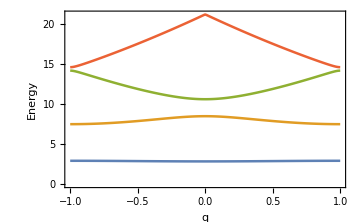

```mathematica
FigBS2=ListPlot[Table[Transpose[{qlist,EnergyMx[[All,iband]]}],{iband,1,nband}],Frame->True,FrameLabel->{"q","Energy"}](*listplot is fast*)
```

#### Band gap - calculated from the band structure

```mathematica
BandGapMin=Table[Min[EnergyMx[[All,jband]]-EnergyMx[[All,1]]],{jband,2,nband}];(*band gap between 1st and 2nd, 3rd, ..nth band*)
BandGapMax=Table[Max[EnergyMx[[All,jband]]-EnergyMx[[All,1]]],{jband,2,nband}];(*max band gap ..*)
BandGapMean=Table[Mean[EnergyMx[[All,jband]]-EnergyMx[[All,1]]],{jband,2,nband}];(*mean band gap ..*)
BandGapTb=Transpose[{BandGapMin,BandGapMax,BandGapMean}];
```

```mathematica
BandGapTbLabel=MapThread[Prepend,{Prepend[BandGapTb,{"Min","Max","Mean"}],Prepend[Table["1-"<>ToString[j],{j,2,nband}],"Band Gap"]}];
Grid[BandGapTbLabel,Dividers->{False,All}]
```

Band Gap | Min | Max | Mean
1-2 | 4.57226 | 5.64555 | 5.0517
1-3 | 7.76612 | 11.262 | 9.19761
1-4 | 11.6885 | 18.3479 | 14.7373

#### Tunneling - calculated from the band width

```mathematica
BandMax=Map[Max[EnergyMx[[All,#]]]&,Range[1,nband]];(*find the max energy for each band*)
BandMin=Map[Min[EnergyMx[[All,#]]]&,Range[1,nband]];(*find the min energy for each band*)
BandWidth = BandMax-BandMin;(*band width for each band*)
```

```mathematica
Tunneling=BandWidth/4(*refer to Jaksch's PRL paper in 1998 and Rev.Mod.Phys.80, which is valid for bands if the trap depth is deeper than the band energy*)
```

{0.0191867,0.249136,0.893167,1.64567}

```mathematica
Grid[Transpose[{Table["Band"<>ToString[j],{j,1,nband}],Tunneling}],Dividers->{False,All}]
```

Band1 | 0.0191867
Band2 | 0.249136
Band3 | 0.893167
Band4 | 1.64567

#### Analytical Approximated Result

##### Band Gap - based on oscillation freq

```mathematica
BandGapApprox[V_]:=√(4*V);(*Trap depth V here is in units of Er*)
```

```mathematica
BandGapApprox[Vlat]//N(*Bascially the band gap btw 1st and 2nd is the ℏω. It works well for deep lattice*)
```

6.32456

##### Tunnelling - calculated from 1D Mathieu equation

```mathematica
Jmathieu[V_]:=4/(√π)V^(3/4)Exp[-2 V^(1/2)];(*1D Mathieu equation, works quite well for V>15Er. Ref. Rev.Mod.Phys.80,885 (2008). Here V is in units of Er*)
```

```mathematica
Jmathieu[Vlat]//N(*1st Band*)
```

0.0227387

## Bloch wave functions

```mathematica
EV[V_,q_,l_]:=Sort[Transpose[Chop[N[Eigensystem[H[V,q]]]]]] [[l,2]] ;(*Eigenstates: results are cacheds for efficiency*)
EVNormed[V_,q_,l_]:=Module[{tmp=EV[V,q,l]},(tmp/Norm[tmp])] ;
```

```mathematica
Bloch[x_,V_,q_,l_]:=Sum[Exp[π*I (q+2n) x]*EVNormed[V,q,l][[n+jMax+1]],{n,-jMax,jMax}];(*should we use cutoff jMax or smaller one instead??*)
```

Note 1:  We want to plot this function typically for many values of x, therefore it is most efficient if we let Mathematica calculate the sum ones analytically, and then insert the right value for x in the finished expression. Therefore we always define a helper function B which we then plot. (There are many other, more elegant ways ..)
Note 2 : For the odd Bloch bands the wave functions are mostly real, so we can plot them right away, but for the even bands they are mostly imaginary, therefore we first multiply them with I. This is not always true for q!=0. We need the phasefactor discussed in the wannier function part.

```mathematica
BRe[x_]={Re[ Bloch[x,Vlat,0,1]],Re[ Bloch[x,10,0,2]]};
BIm[x_]={Im[ Bloch[x,Vlat,0,1]],Im[ Bloch[x,10,0,2]]};
BNorm[x_]={Re[ Bloch[x,Vlat,0,1]],Re[I Bloch[x,10,0,2]]};
```

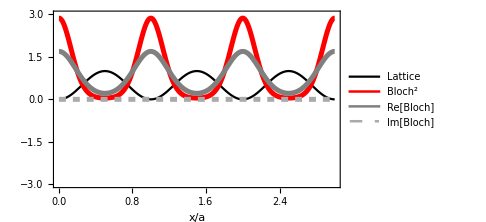
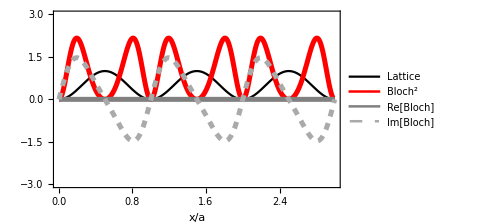

```mathematica
Table[Plot[{Sin[π*x]^2,(BNorm[x]^2)[[i]],BRe[x][[i]],BIm[x][[i]]},{x,0,3},Frame->True,Axes->False,FrameLabel->{"x/a"},PlotRange->{-3,3},PlotLegends->{"Lattice","Bloch^2","Re[Bloch]","Im[Bloch]"},PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Gray},{Thickness[0.01],Dashed,Lighter[Gray]}}],{i,1,2}](*Bloch waves of 1st and 2nd band at q=0*)
```

## Wannier functions

Note1: Ref. W. Kohn. Analytic properties of bloch waves and wannier functions (1959).
Note2: Even though the sum of Bloch[q] and Bloch[-q] is either real or imaginary, wannier function cannot be  calculated by summing Bloch waves up simply with the phase factor like  ⅈ + or -. We do need the phasefactor function.

```mathematica
PhaseFactor[V_,q_,l_]:=If[OddQ[l],Arg[Bloch[0,V,q,l]],Arg[Bloch[0.25,V,q,l]]];(*force phase at x=0 equals to 0 for every Bloch waves for odd band and phase at x=0.25 (or values close to 0.13) equals to 0 for even band. It just Works!!*)
```

```mathematica
qqstep=0.1;
Wannier[x_,V_,l_,xi_]:=Sum[Exp[π*I*q*(-xi)]*Exp[-I*PhaseFactor[V,q,l]]*Bloch[x,V,q,l],{q,-1,1,qqstep}]*(qqstep/2)-1/2(Sum[Exp[π*I*q*(-xi)]*Exp[-I*PhaseFactor[V,q,l]]*Bloch[x,V,q,l],{q,-1,1,2}])*(qqstep/2)

(*numerically integrate q from -1 to 1, however -1 and 1 are the same and we should deduct one*)
(*x: position, V: lattice depth, l: nth band, xi: wannier function at lattice site xi, which should be an integer*)
(*Wannier[x_,V_,l_,xi_]:=Sum[Exp[π*I*q*(-xi)]*SignFactor[V,q,l]*Bloch[x,V,q,l],{q,-1,1,qqstep}]*(qqstep/2)-1/2(Sum[Exp[π*I*q*(-xi)]*SignFactor[V,q,l]*Bloch[x,V,q,l],{q,-1,1,2}])*(qqstep/2)*)
```

```mathematica
nWannier=2;(*1st, 2nd, 3rd band*)
```

```mathematica
xxstep=0.01;xlist=Range[-5,5,xxstep];
wlist = Wannier[xlist,Vlat,nWannier,0];
ltslist=Sin[π*xlist]^2;(*lattice potential*)
```

```mathematica
wlistNorm=wlist/√Total[Re[wlist]^2*xxstep];(*Normalize the wannier function. Here wannier function is assumed to be real*)
```

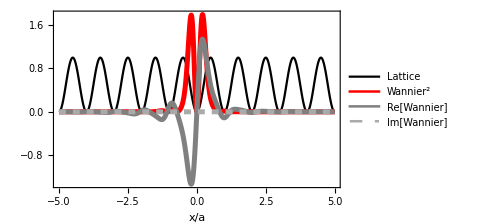

```mathematica
ListPlot[{Transpose[{xlist,ltslist}],Transpose[{xlist,Re[wlistNorm]^2}],Transpose[{xlist,Re[wlistNorm]}],Transpose[{xlist,Im[wlistNorm]}]},FrameLabel->{"x/a"},Frame->True,PlotLegends->{"Lattice","Wannier^2","Re[Wannier]","Im[Wannier]"},PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Gray},{Thickness[0.01],Dashed,Lighter[Gray]}}]
```

## Hubbard parameters

```mathematica
λLatK39=725*10^-9;(*725 lattice wavelength*)
```

```mathematica
k0K39=(2π)/λLatK39;(*lattice wave number*)
```

```mathematica
ErK39=ℏ^2 k0K39^2/(2*mK39);(*recoil energy*)
```

```mathematica
gcontact=(4π ℏ^2)/mK39*aK39;
```

#### Interaction U

```mathematica
Uint=gcontact/ErK39*(π/k0K39)^-3*Total[(Re[wlist])^4*xxstep]^3(*for 3D cubic lattice in units of Er*)
```

0.0981664

#### Tunneling J - using wannier functions

```mathematica
wlist2 = Wannier[xlist,Vlat,nWannier,1];(*wannier function at x=1, nearest neighbor*)
```

```mathematica
wlistNorm2=wlist2/√Total[Re[wlist2]^2*xxstep];(*Normalize the wannier function. Here wannier function is assumed to be real*)
```

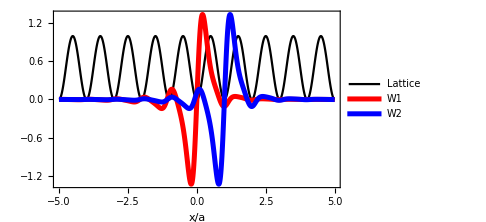

```mathematica
ListPlot[{Transpose[{xlist,ltslist}],Transpose[{xlist,Re[wlistNorm]}],Transpose[{xlist,Re[wlistNorm2]}]},FrameLabel->{"x/a"},Frame->True,PlotLegends->{"Lattice","W1","W2"},PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Blue}}]
```

```mathematica
dwlist=(wlist[[1;;-3]]+wlist[[3;;-1]]-2*wlist[[2;;-2]])/xxstep^2/π^2;(*-ℏ^2/(2m)∂/(∂^2 x) in Hamiltonian and here we use Er as units and wannier function is dimensionless, -ℏ^2/(2m)∂/(∂^2 x)=-(ℏ^2 a^2)/(2m)∂/(∂^2 (x/a))= -(ℏ^2 k0^2)/(2m)∂/(∂^2 (x/a))1/π^2=Er ∂/(∂^2 (x/a))1/π^2*)
```

```mathematica
Jhop=(Chop[-Total[Re[wlist2[[2;;-2]]]*Re[dwlist]*xxstep]+Total[Vlat*ltslist*Re[wlist]*Re[wlist2]*xxstep]])(*Lattice tunnelling elements in units of Er. This result is consistent with the value of bandwidth/4*)
```

0.243286

##### next-nearest-neighbor hopping

```mathematica
wlist3 = Wannier[xlist,Vlat,nWannier,2];(*wannier function at x=2, next nearest neighbor*)
```

```mathematica
wlistNorm3=wlist3/√Total[Re[wlist2]^2*xxstep];(*Normalize the wannier function. Here wannier function is assumed to be real*)
```

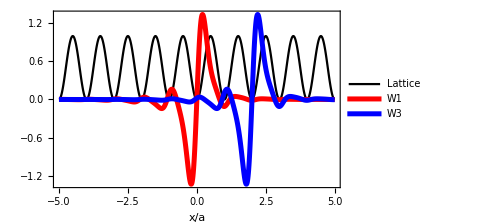

```mathematica
ListPlot[{Transpose[{xlist,ltslist}],Transpose[{xlist,Re[wlistNorm]}],Transpose[{xlist,Re[wlistNorm3]}]},FrameLabel->{"x/a"},Frame->True,PlotLegends->{"Lattice","W1","W3"},PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Blue}}]
```

```mathematica
Jhop2=(Chop[-Total[Re[wlist3[[2;;-2]]]*Re[dwlist]*xxstep]+Total[Vlat*ltslist*Re[wlist]*Re[wlist3]*xxstep]])(*Lattice tunnelling elements in units of Er. This result is consistent with this value of bandwidth/4*)
```

0.026208

#### Ratio U/J

```mathematica
Uint/Jhop(*Ratio btw interaction energy and hopping*)
```

0.403503